Dynamic  Mean-Variance Portfolio Selection With No-Shorting Constraints

Given Data:
number of asset m = 3
Interest rate of bond r = 0.02
Interest rates of assets B = (0.04, 0.05, (0.06))^T
Volatility Matrix 
σ  =  1 | 0 | 2/3
0 | 1 | 0
0 | 0 | 2/3

σ^-1 = 1 | 0 | -1
0 | 1 | 0
0 | 0 | 3/2

Step 1: We will calculate Appreciation rate

```mathematica
m = 3
r = 0.02
B = {{0.04}, {0.05}, {0.06}}
Bd = B - r
sigma = {{1, 0, 2/3}, {0,1,0}, {0,0,2/3}}
sigmaI = Inverse[sigma]
```

3

0.02

{{0.04},{0.05},{0.06}}

{{0.02},{0.03},{0.04}}

{{1,0,2/3},{0,1,0},{0,0,2/3}}

{{1,0,-1},{0,1,0},{0,0,3/2}}

Step 2: Calculate the value of theta

```mathematica
theta = sigmaI.Bd
```

{{-0.02},{0.03},{0.06}}

Step 3: Calculate the value of π̄ with this formula:

S(π) = 1/2 ||σ^-1 π + θ(||)^2, 
	where π̄ is the unique minimizer of S(π).

```mathematica
pi = {{x},{y}, {z}}
spi = sigmaI.pi + theta
```

{{x},{y},{z}}

{{-0.02+x-z},{0.03+y},{0.06+(3 z)/2}}

```mathematica
spi = Flatten[spi]
```

{-0.02+x-z,0.03+y,0.06+(3 z)/2}

```mathematica
spi = Total[spi^2]
```

(0.03+y)^2+(-0.02+x-z)^2+(0.06+(3 z)/2)^2

```mathematica
spi = 0.5*spi
```

0.5 ((0.03+y)^2+(-0.02+x-z)^2+(0.06+(3 z)/2)^2)

```mathematica
pibar  =ArgMin[{spi, {x,y,z}>=0 }, {x, y, z} ]
```

{0.0200001,4.50484×10^-8,1.50156×10^-8}

Step 4: We will calculate S(π̄) using:
S(π̄) = 1/2 ||σ^-1 π̄ + θ(||)^2

```mathematica
spibar = sigmaI.pibar + theta
spibar =  Flatten[spibar]
spibar = spibar^2
spibar  =Total[spibar]
spibar = spibar * 0.5
```

{{6.7573×10^-8},{0.03},{0.06}}

{6.7573×10^-8,0.03,0.06}

{4.56612×10^-15,0.000900003,0.0036}

0.00450001

0.00225

Step 5: Calculate the value of ||θ(||)^2
S(π̄) =||σ^-1 π̄ + θ(||)^2

```mathematica
thetaSquare = spibar * 2
```

0.00450001

Step 6: 
Calculate the  value of  ((σσ')^-1) [π̄ + (b - rI)]

```mathematica
utx = Inverse[sigma.Transpose[sigma]].(pibar + Bd)
utx
```

{{6.7573×10^-8},{0.03},{0.09}}

{{6.7573×10^-8},{0.03},{0.09}}

Step 7: Plotting Efficient Frontier

1

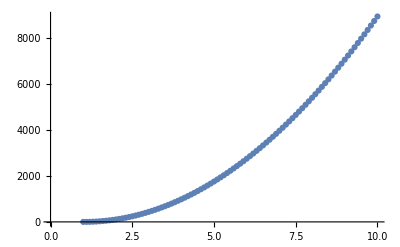

```mathematica
x0 = 1
x = Range[1, 10, 0.1];
y = N[((x-x0*ⅇ^(1/50))/(√(-1+ⅇ^(9/1000))))^2]  ;
data=Transpose@{x,y};
ListPlot[data, PlotStyle->Thick]
```